```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

```mathematica
attens={0.2778,0.3207,1.205,1.593,1.060,0.2570,0.9639,1.760,0.7661,1.512};
percentages={{0.871,0.914},{0,0.004},{0,0.005},{0.012,0.02},{0,0.003},{0.021,0.029},{0.0018,0.0029},{0.051,0.061},{0,0.002},{0,0.0005}};
n=Length[attens];
```

```mathematica
trials=1000000;
randomperc=Table[RandomReal[percentages[[i]],trials],{i,n}];
mus=Sum[randomperc[[i]]*attens[[i]],{i,n}]/Sum[randomperc[[i]],{i,n}];
```

```mathematica
b=20;bins=HistogramList[mus,b];
model=NonlinearModelFit[Table[{(bins[[1,i]]+bins[[1,i+1]])/2,bins[[2,i]]},{i,Length[bins[[2]]]}],a Exp[-1/2((x-μ)/σ)^2],{{a,140000},{μ,0.385},{σ,0.1}},x];
model["ParameterTable"]
Print["Percent Error = ",100*model["BestFitParameters"][[3,2]]/model["BestFitParameters"][[2,2]]]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 143579. | 1913.68 | 75.0276 | 9.7921×10^-21
μ | 0.387399 | 0.0000872445 | 4440.38 | 2.60642×10^-47
σ | 0.00566958 | 0.000087308 | 64.9377 | 8.4919×10^-20

Percent Error = 1.4635

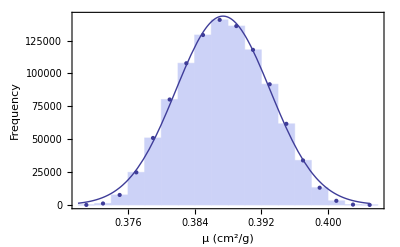

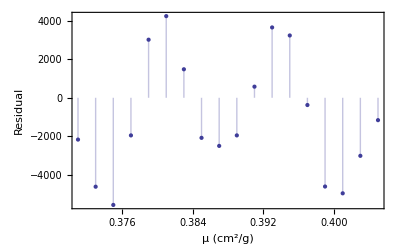

```mathematica
fontsize=12;imagesize=400;imagedpi=300;
Show[
Histogram[mus,b,PlotTheme->"Classic"],
ListPlot[Table[{(bins[[1,i]]+bins[[1,i+1]])/2,bins[[2,i]]},{i,Length[bins[[2]]]}],PlotTheme->"Classic"],
Plot[model["BestFit"],{x,0.370,0.405},PlotRange->All,PlotTheme->"Classic"],

ImageSize->imagesize,
FrameLabel->{"μ (cm^2/g)","Frequency"},
Frame->{{True,False},{True,False}},
Axes->False,
BaseStyle->{FontSize->fontsize}
]
Export["../Thesis/Draft/Figures/montecarlo.png",%,ImageResolution->imagedpi];

ListPlot[Table[{(bins[[1,i]]+bins[[1,i+1]])/2,model["FitResiduals"][[i]]},{i,Length[bins[[2]]]}],

ImageSize->imagesize,
FrameLabel->{"μ (cm^2/g)","Residual"},
PlotTheme->"Classic",
Filling->Axis,
Frame->{{True,False},{True,False}},
Axes->True,
BaseStyle->{FontSize->fontsize}
]
```

```mathematica
Print["Mean = ",Mean[mus]]
Print["Standard Deviation = ",StandardDeviation[mus]]
Print["Percent Error = ",100*StandardDeviation[mus]/Mean[mus]]
```

Mean = 0.3874

Standard Deviation = 0.00522591

Percent Error = 1.34897